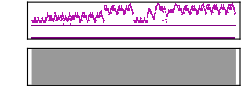

```mathematica
t=120/275.98;

Leap[s_,l_,v_,k_]:=Sound[{SoundNote[s,k l t,"Violin",SoundVolume->v],SoundNote[None,l t-k l t]}];
Vibrato[s_,e_,l_,v_,n_]:=Sound[Table[If[1==Mod[i,2],SoundNote[s,l t/n,"Violin"],SoundNote[e,l t/n,"Violin"]],{i,1,n}],l t,SoundVolume->v];

v=Sound[{
(*1*)
SoundNote["EB4",1.5 t,"Violin"],SoundNote["C#4",0.25 t,"Violin"],SoundNote["D4",0.25 t,"Violin"],SoundNote["EB4",1.5 t,"Violin"],SoundNote["C#4",0.25 t,"Violin"],SoundNote["D4",0.25 t,"Violin"],

(*2*)
SoundNote["EB4",1.5 t,"Violin"],SoundNote["C#4",0.25 t,"Violin"],SoundNote["D4",0.25 t,"Violin"],SoundNote["EB4",0.5 t,"Violin"],SoundNote["EB4",0.25 t,"Violin"],SoundNote["GB4",0.25 t,"Violin"],SoundNote["AB4",0.5 t,"Violin"],SoundNote["GB4",0.25 t,"Violin"],SoundNote["AB4",0.25 t,"Violin"],

(*3*)
SoundNote["EB4",1.5 t,"Violin"],SoundNote["C#4",0.25 t,"Violin"],SoundNote["D4",0.25 t,"Violin"],SoundNote["EB4",1.5 t,"Violin"],SoundNote["C#4",0.25 t,"Violin"],SoundNote["D4",0.25 t,"Violin"],

(*4*)
SoundNote["EB4",1.5 t,"Violin"],SoundNote["C#4",0.25 t,"Violin"],SoundNote["D4",0.25 t,"Violin"],SoundNote["AB4",0.5 t,"Violin"],SoundNote["GB4",0.25 t,"Violin"],SoundNote["AB4",0.25 t,"Violin"],SoundNote["GB4",0.5 t,"Violin"],SoundNote["EB4",0.25 t,"Violin"],SoundNote["GB4",0.25 t,"Violin"],
(*5*)
SoundNote["EB4",1.5 t,"Violin"],SoundNote["C#4",0.25 t,"Violin"],SoundNote["D4",0.25 t,"Violin"],SoundNote["EB4",1.5 t,"Violin"],SoundNote["C#4",0.25 t,"Violin"],SoundNote["D4",0.25 t,"Violin"],
(*6*)
SoundNote["EB4",1.5 t,"Violin"],SoundNote["C#4",0.25 t,"Violin"],SoundNote["D4",0.25 t,"Violin"],SoundNote["EB4",0.5 t,"Violin"],SoundNote["EB4",0.25 t,"Violin"],SoundNote["GB4",0.25 t,"Violin"],SoundNote["AB4",0.5 t,"Violin"],SoundNote["GB4",0.25 t,"Violin"],SoundNote["AB4",0.25 t,"Violin"],
(*7*)
SoundNote["EB4",1.5 t,"Violin"],SoundNote["C#4",0.25 t,"Violin"],SoundNote["D4",0.25 t,"Violin"],SoundNote["EB4",1.5 t,"Violin"],SoundNote["C#4",0.25 t,"Violin"],SoundNote["D4",0.25 t,"Violin"],
(*8*)
SoundNote["EB4",1.5 t,"Violin"],SoundNote["C#4",0.25 t,"Violin"],SoundNote["D4",0.25 t,"Violin"],SoundNote["EB4",t/3,"Violin"],SoundNote["EB4",t/3,"Violin"],SoundNote["GB4",t/3,"Violin"],SoundNote["AB4",t/3,"Violin"],SoundNote["GB4",t/3,"Violin"],SoundNote["AB4",t/3,"Violin"],
(*9*)
SoundNote["EB4",0.5 t,"Violin"],SoundNote["F4",0.5 t,"Violin"],SoundNote["GB4",0.5 t,"Violin"],SoundNote["AB4",0.5 t,"Violin"],SoundNote["BB4",t,"Violin"],SoundNote["EB5",0.5 t,"Violin"],SoundNote["DB5",0.5 t,"Violin"],
(*10*)
SoundNote["BB4",t,"Violin"],SoundNote["EB4",t,"Violin"],SoundNote["BB4",0.5 t,"Violin"],SoundNote["AB4",0.5 t,"Violin"],SoundNote["GB4",0.5 t,"Violin"],SoundNote["F4",0.5 t,"Violin"],
(*11*)
SoundNote["EB4",0.5 t,"Violin"],SoundNote["F4",0.5 t,"Violin"],SoundNote["GB4",0.5 t,"Violin"],SoundNote["AB4",0.5 t,"Violin"],SoundNote["BB4",t,"Violin"],SoundNote["AB4",0.5 t,"Violin"],SoundNote["GB4",0.5 t,"Violin"],
(*12*)
SoundNote["F4",0.5 t,"Violin"],SoundNote["EB4",0.5 t,"Violin"],SoundNote["F4",0.5 t,"Violin"],SoundNote["GB4",0.5 t,"Violin"],SoundNote["F4",0.5 t,"Violin"],SoundNote["EB4",0.5 t,"Violin"],SoundNote["D4",0.5 t,"Violin"],SoundNote["F4",0.5 t,"Violin"],
(*13*)
SoundNote["EB4",0.5 t,"Violin"],SoundNote["F4",0.5 t,"Violin"],SoundNote["GB4",0.5 t,"Violin"],SoundNote["AB4",0.5 t,"Violin"],SoundNote["BB4",t,"Violin"],SoundNote["EB5",0.5 t,"Violin"],SoundNote["DB5",0.5 t,"Violin"],
(*14*)
SoundNote["BB4",t,"Violin"],SoundNote["EB4",t,"Violin"],SoundNote["BB4",0.5 t,"Violin"],SoundNote["AB4",0.5 t,"Violin"],SoundNote["GB4",0.5 t,"Violin"],SoundNote["F4",0.5 t,"Violin"],
(*15*)
SoundNote["EB4",0.5 t,"Violin"],SoundNote["F4",0.5 t,"Violin"],SoundNote["GB4",0.5 t,"Violin"],SoundNote["AB4",0.5 t,"Violin"],SoundNote["BB4",t,"Violin"],SoundNote["AB4",0.5 t,"Violin"],SoundNote["GB4",0.5 t,"Violin"],
(*16*)
SoundNote["F4",t,"Violin"],SoundNote["GB4",t,"Violin"],SoundNote["AB4",t,"Violin"],SoundNote["BB4",t,"Violin"],
(*17*)
SoundNote["EB4",0.5 t,"Violin"],SoundNote["F4",0.5 t,"Violin"],SoundNote[{"GB4","EB4"},0.5 t,"Violin"],SoundNote[{"AB4","F4"},0.5 t,"Violin"],SoundNote[{"BB4","GB4"},t,"Violin"],SoundNote[{"EB5","GB4"},0.5 t,"Violin"],SoundNote[{"DB5","BB4"},0.5 t,"Violin"],
(*18*)
SoundNote[{"BB4","GB4"},t,"Violin"],SoundNote[{"EB4","BB3"},t,"Violin"],SoundNote["BB4",0.5 t,"Violin"],SoundNote["AB4",0.5 t,"Violin"],SoundNote["GB4",0.5 t,"Violin"],SoundNote["F4",0.5 t,"Violin"],
(*19*)
SoundNote["EB4",0.5 t,"Violin"],SoundNote["F4",0.5 t,"Violin"],SoundNote["GB4",0.5 t,"Violin"],SoundNote["AB4",0.5 t,"Violin"],SoundNote["BB4",t,"Violin"],SoundNote["AB4",0.5 t,"Violin"],SoundNote["GB4",0.5 t,"Violin"],
(*20*)
SoundNote["F4",0.5 t,"Violin"],SoundNote["EB4",0.5 t,"Violin"],SoundNote["F4",0.5 t,"Violin"],SoundNote["GB4",0.5 t,"Violin"],SoundNote["F4",0.5 t,"Violin"],SoundNote["EB4",0.5 t,"Violin"],SoundNote["D4",0.5 t,"Violin"],SoundNote["F4",0.5 t,"Violin"],
(*21*)
SoundNote["EB4",0.5 t,"Violin"],SoundNote["F4",0.5 t,"Violin"],SoundNote[{"GB4","EB4"},0.5 t,"Violin"],SoundNote[{"AB4","F4"},0.5 t,"Violin"],SoundNote[{"BB4","GB4"},t,"Violin"],SoundNote[{"EB5","GB4"},0.5 t,"Violin"],SoundNote[{"DB5","BB4"},0.5 t,"Violin"],
(*22*)
SoundNote[{"BB4","GB4"},t,"Violin"],SoundNote[{"EB4","BB3"},t,"Violin"],SoundNote["BB4",0.5 t,"Violin"],SoundNote["AB4",0.5 t,"Violin"],SoundNote["GB4",0.5 t,"Violin"],SoundNote["F4",0.5 t,"Violin"],
(*23*)
SoundNote["EB4",0.5 t,"Violin"],SoundNote["F4",0.5 t,"Violin"],SoundNote["GB4",0.5 t,"Violin"],SoundNote["AB4",0.5 t,"Violin"],SoundNote["BB4",t,"Violin"],SoundNote["AB4",0.5 t,"Violin"],SoundNote["GB4",0.5 t,"Violin"],
(*24*)
SoundNote["F4",t,"Violin"],SoundNote["GB4",t,"Violin"],SoundNote["AB4",t,"Violin"],SoundNote["BB4",t,"Violin"],
(*25*)
SoundNote["DB5",0.5 t,"Violin"],SoundNote["EB5",0.5 t,"Violin"],SoundNote["BB4",0.5 t,"Violin"],SoundNote["AB4",0.5 t,"Violin"],SoundNote["BB4",t,"Violin"],SoundNote["AB4",0.5 t,"Violin"],SoundNote["BB4",0.5 t,"Violin"],
(*26*)
SoundNote["DB5",0.5 t,"Violin"],SoundNote["EB5",0.5 t,"Violin"],SoundNote["BB4",0.5 t,"Violin"],SoundNote["AB4",0.5 t,"Violin"],SoundNote["BB4",t,"Violin"],SoundNote["AB4",0.5 t,"Violin"],SoundNote["BB4",0.5 t,"Violin"],
(*27*)
SoundNote["AB4",0.5 t,"Violin"],SoundNote["GB4",0.5 t,"Violin"],SoundNote["F4",0.5 t,"Violin"],SoundNote["DB4",0.5 t,"Violin"],SoundNote["EB4",t,"Violin"],SoundNote["DB4",0.5 t,"Violin"],SoundNote["EB4",0.5 t,"Violin"],
(*28*)
SoundNote["F4",0.5 t,"Violin"],SoundNote["GB4",0.5 t,"Violin"],SoundNote["AB4",0.5 t,"Violin"],SoundNote["BB4",0.5 t,"Violin"],SoundNote["EB4",t,"Violin"],SoundNote["BB4",0.5 t,"Violin"],SoundNote["DB5",0.5 t,"Violin"],
(*R25*)
SoundNote["DB5",0.5 t,"Violin"],SoundNote["EB5",0.5 t,"Violin"],SoundNote["BB4",0.5 t,"Violin"],SoundNote["AB4",0.5 t,"Violin"],SoundNote["BB4",t,"Violin"],SoundNote["AB4",0.5 t,"Violin"],SoundNote["BB4",0.5 t,"Violin"],
(*R26*)
SoundNote["DB5",0.5 t,"Violin"],SoundNote["EB5",0.5 t,"Violin"],SoundNote["BB4",0.5 t,"Violin"],SoundNote["AB4",0.5 t,"Violin"],SoundNote["BB4",t,"Violin"],SoundNote["AB4",0.5 t,"Violin"],SoundNote["BB4",0.5 t,"Violin"],
(*R27*)
SoundNote["AB4",0.5 t,"Violin"],SoundNote["GB4",0.5 t,"Violin"],SoundNote["F4",0.5 t,"Violin"],SoundNote["DB4",0.5 t,"Violin"],SoundNote["EB4",t,"Violin"],SoundNote["DB4",0.5 t,"Violin"],SoundNote["EB4",0.5 t,"Violin"],
(*R28*)
SoundNote["F4",0.5 t,"Violin"],SoundNote["GB4",0.5 t,"Violin"],SoundNote["AB4",0.5 t,"Violin"],SoundNote["BB4",0.5 t,"Violin"],SoundNote["EB4",t,"Violin"],SoundNote["BB4",0.5 t,"Violin"],SoundNote["DB5",0.5 t,"Violin"],
(*29*)
SoundNote["DB5",0.5 t,"Violin"],SoundNote["EB5",0.5 t,"Violin"],SoundNote["BB4",0.5 t,"Violin"],SoundNote["AB4",0.5 t,"Violin"],SoundNote["BB4",t,"Violin"],SoundNote["AB4",0.5 t,"Violin"],SoundNote["BB4",0.5 t,"Violin"],
(*30*)
SoundNote["DB5",0.5 t,"Violin"],SoundNote["EB5",0.5 t,"Violin"],SoundNote["BB4",0.5 t,"Violin"],SoundNote["AB4",0.5 t,"Violin"],SoundNote["BB4",t,"Violin"],SoundNote["AB4",0.5 t,"Violin"],SoundNote["BB4",0.5 t,"Violin"],
(*31*)
SoundNote["AB4",0.5 t,"Violin"],SoundNote["GB4",0.5 t,"Violin"],SoundNote["F4",0.5 t,"Violin"],SoundNote["DB4",0.5 t,"Violin"],SoundNote["EB4",t,"Violin"],SoundNote["DB4",0.5 t,"Violin"],SoundNote["EB4",0.5 t,"Violin"],
(*32*)
SoundNote["F4",0.5 t,"Violin"],SoundNote["GB4",0.5 t,"Violin"],SoundNote["AB4",0.5 t,"Violin"],SoundNote["BB4",0.5 t,"Violin"],SoundNote["EB4",t,"Violin"],SoundNote["BB4",0.5 t,"Violin"],SoundNote["DB5",0.5 t,"Violin"],
(*33*)
SoundNote["DB5",0.5 t,"Violin"],SoundNote["EB5",0.5 t,"Violin"],SoundNote["BB4",0.5 t,"Violin"],SoundNote["AB4",0.5 t,"Violin"],SoundNote["BB4",t,"Violin"],SoundNote["AB4",0.5 t,"Violin"],SoundNote["BB4",0.5 t,"Violin"],
(*34*)
SoundNote["DB5",0.5 t,"Violin"],SoundNote["EB5",0.5 t,"Violin"],SoundNote["BB4",0.5 t,"Violin"],SoundNote["AB4",0.5 t,"Violin"],SoundNote["BB4",t,"Violin"],SoundNote["EB5",0.5 t,"Violin"],SoundNote["F5",0.5 t,"Violin"],
(*35*)
SoundNote["GB5",0.5 t,"Violin"],SoundNote["F5",0.5 t,"Violin"],SoundNote["EB5",0.5 t,"Violin"],SoundNote["DB5",0.5 t,"Violin"],SoundNote["BB4",t,"Violin"],SoundNote["AB4",0.5 t,"Violin"],SoundNote["BB4",0.5 t,"Violin"],
(*36*)
SoundNote["AB4",0.5 t,"Violin"],SoundNote["GB4",0.5 t,"Violin"],SoundNote["F4",0.5 t,"Violin"],SoundNote["DB4",0.5 t,"Violin"],SoundNote["EB4",t,"Violin"],SoundNote["BB5",0.5 t,"Violin"],SoundNote["DB6",0.5 t,"Violin"],
(*37*)
SoundNote["DB6",0.5 t,"Violin"],SoundNote["EB6",0.5 t,"Violin"],SoundNote["BB5",0.5 t,"Violin"],SoundNote["AB5",0.5 t,"Violin"],SoundNote["BB5",t,"Violin"],SoundNote["AB5",0.5 t,"Violin"],SoundNote["BB5",0.5 t,"Violin"],
(*38*)
SoundNote["DB6",0.5 t,"Violin"],SoundNote["EB6",0.5 t,"Violin"],SoundNote["BB5",0.5 t,"Violin"],SoundNote["AB5",0.5 t,"Violin"],SoundNote["BB5",t,"Violin"],SoundNote["AB5",0.5 t,"Violin"],SoundNote["BB5",0.5 t,"Violin"],
(*39*)
SoundNote["AB5",0.5 t,"Violin"],SoundNote["GB5",0.5 t,"Violin"],SoundNote["F5",0.5 t,"Violin"],SoundNote["DB5",0.5 t,"Violin"],SoundNote["EB5",t,"Violin"],SoundNote["DB5",0.5 t,"Violin"],SoundNote["EB5",0.5 t,"Violin"],
(*40*)
SoundNote["F5",0.5 t,"Violin"],SoundNote["GB5",0.5 t,"Violin"],SoundNote["AB5",0.5 t,"Violin"],SoundNote["BB5",0.5 t,"Violin"],SoundNote["EB5",t,"Violin"],SoundNote["BB5",0.5 t,"Violin"],SoundNote["DB6",0.5 t,"Violin"],
(*R37*)
SoundNote["DB6",0.5 t,"Violin"],SoundNote["EB6",0.5 t,"Violin"],SoundNote["BB5",0.5 t,"Violin"],SoundNote["AB5",0.5 t,"Violin"],SoundNote["BB5",t,"Violin"],SoundNote["AB5",0.5 t,"Violin"],SoundNote["BB5",0.5 t,"Violin"],
(*R38*)
SoundNote["DB6",0.5 t,"Violin"],SoundNote["EB6",0.5 t,"Violin"],SoundNote["BB5",0.5 t,"Violin"],SoundNote["AB5",0.5 t,"Violin"],SoundNote["BB5",t,"Violin"],SoundNote["AB5",0.5 t,"Violin"],SoundNote["BB5",0.5 t,"Violin"],
(*R39*)
SoundNote["AB5",0.5 t,"Violin"],SoundNote["GB5",0.5 t,"Violin"],SoundNote["F5",0.5 t,"Violin"],SoundNote["DB5",0.5 t,"Violin"],SoundNote["EB5",t,"Violin"],SoundNote["DB5",0.5 t,"Violin"],SoundNote["EB5",0.5 t,"Violin"],
(*R40*)
SoundNote["F5",0.5 t,"Violin"],SoundNote["GB5",0.5 t,"Violin"],SoundNote["AB5",0.5 t,"Violin"],SoundNote["BB5",0.5 t,"Violin"],SoundNote["EB5",t,"Violin"],SoundNote["BB5",0.5 t,"Violin"],SoundNote["DB6",0.5 t,"Violin"],
(*41*)
SoundNote["DB6",0.5 t,"Violin"],SoundNote["EB6",0.5 t,"Violin"],SoundNote["BB5",0.5 t,"Violin"],SoundNote["AB5",0.5 t,"Violin"],SoundNote["BB5",t,"Violin"],SoundNote["AB5",0.5 t,"Violin"],SoundNote["BB5",0.5 t,"Violin"],
(*42*)
SoundNote["DB6",0.5 t,"Violin"],SoundNote["EB6",0.5 t,"Violin"],SoundNote["BB5",0.5 t,"Violin"],SoundNote["AB5",0.5 t,"Violin"],SoundNote["BB5",t,"Violin"],SoundNote["AB5",0.5 t,"Violin"],SoundNote["BB5",0.5 t,"Violin"],
(*43*)
SoundNote["AB5",0.5 t,"Violin"],SoundNote["GB5",0.5 t,"Violin"],SoundNote["F5",0.5 t,"Violin"],SoundNote["DB5",0.5 t,"Violin"],SoundNote["EB5",t,"Violin"],SoundNote["DB5",0.5 t,"Violin"],SoundNote["EB5",0.5 t,"Violin"],
(*44*)
SoundNote["F5",0.5 t,"Violin"],SoundNote["GB5",0.5 t,"Violin"],SoundNote["AB5",0.5 t,"Violin"],SoundNote["BB5",0.5 t,"Violin"],SoundNote["EB5",t,"Violin"],SoundNote["BB5",0.5 t,"Violin"],SoundNote["DB6",0.5 t,"Violin"],
(*45*)
SoundNote["DB6",0.5 t,"Violin"],SoundNote["EB6",0.5 t,"Violin"],SoundNote["BB5",0.5 t,"Violin"],SoundNote["AB5",0.5 t,"Violin"],SoundNote["BB5",t,"Violin"],SoundNote["AB5",0.5 t,"Violin"],SoundNote["BB5",0.5 t,"Violin"],
(*46*)
SoundNote["DB6",0.5 t,"Violin"],SoundNote["EB6",0.5 t,"Violin"],SoundNote["BB5",0.5 t,"Violin"],SoundNote["AB5",0.5 t,"Violin"],SoundNote["BB5",t,"Violin"],SoundNote["EB6",0.5 t,"Violin"],SoundNote["F6",0.5 t,"Violin"],
(*47*)
SoundNote["GB6",0.5 t,"Violin"],SoundNote["F6",0.5 t,"Violin"],SoundNote["EB6",0.5 t,"Violin"],SoundNote["DB6",0.5 t,"Violin"],SoundNote["BB5",t,"Violin"],SoundNote["AB5",0.5 t,"Violin"],SoundNote["BB5",0.5 t,"Violin"],
(*48*)
Leap["AB5",0.5,1,0.75],Leap["GB5",0.5,1,0.75],Leap["F5",0.5,1,0.75],Leap["DB5",0.5,1,0.75],SoundNote["EB5",t,"Violin"],SoundNote[None,t],
(*49*)
SoundNote["EB4",1.5 t,"Violin"],SoundNote["C#4",0.25 t,"Violin"],SoundNote["D4",0.25 t,"Violin"],SoundNote["EB4",1.5 t,"Violin"],SoundNote["C#4",0.25 t,"Violin"],SoundNote["D4",0.25 t,"Violin"],

(*50*)
SoundNote["EB4",1.5 t,"Violin"],SoundNote["C#4",0.25 t,"Violin"],SoundNote["D4",0.25 t,"Violin"],SoundNote["EB4",0.5 t,"Violin"],SoundNote["EB4",0.25 t,"Violin"],SoundNote["GB4",0.25 t,"Violin"],SoundNote["AB4",0.5 t,"Violin"],SoundNote["GB4",0.25 t,"Violin"],SoundNote["AB4",0.25 t,"Violin"],

(*51*)
SoundNote["EB4",1.5 t,"Violin"],SoundNote["C#4",0.25 t,"Violin"],SoundNote["D4",0.25 t,"Violin"],SoundNote["EB4",1.5 t,"Violin"],SoundNote["C#4",0.25 t,"Violin"],SoundNote["D4",0.25 t,"Violin"],

(*52*)
SoundNote["EB4",1.5 t,"Violin"],SoundNote["C#4",0.25 t,"Violin"],SoundNote["D4",0.25 t,"Violin"],SoundNote["AB4",0.5 t,"Violin"],SoundNote["GB4",0.25 t,"Violin"],SoundNote["AB4",0.25 t,"Violin"],SoundNote["GB4",0.5 t,"Violin"],SoundNote["EB4",0.25 t,"Violin"],SoundNote["GB4",0.25 t,"Violin"],
(*53*)
SoundNote["EB4",1.5 t,"Violin"],SoundNote["C#4",0.25 t,"Violin"],SoundNote["D4",0.25 t,"Violin"],SoundNote["EB4",1.5 t,"Violin"],SoundNote["C#4",0.25 t,"Violin"],SoundNote["D4",0.25 t,"Violin"],
(*54*)
SoundNote["EB4",1.5 t,"Violin"],SoundNote["C#4",0.25 t,"Violin"],SoundNote["D4",0.25 t,"Violin"],SoundNote["EB4",0.5 t,"Violin"],SoundNote["EB4",0.25 t,"Violin"],SoundNote["GB4",0.25 t,"Violin"],SoundNote["AB4",0.5 t,"Violin"],SoundNote["GB4",0.25 t,"Violin"],SoundNote["AB4",0.25 t,"Violin"],
(*55*)
SoundNote["EB4",1.5 t,"Violin"],SoundNote["C#4",0.25 t,"Violin"],SoundNote["D4",0.25 t,"Violin"],SoundNote["EB4",1.5 t,"Violin"],SoundNote["C#4",0.25 t,"Violin"],SoundNote["D4",0.25 t,"Violin"],
(*56*)
SoundNote["EB4",1.5 t,"Violin"],SoundNote["C#4",0.25 t,"Violin"],SoundNote["D4",0.25 t,"Violin"],SoundNote["AB4",t/3,"Violin"],SoundNote["BB4",t/3,"Violin"],SoundNote["DB5",t/3,"Violin"],SoundNote["EB5",t/3,"Violin"],SoundNote["GB5",t/3,"Violin"],SoundNote["BB5",t/3,"Violin"],
(*57*)
SoundNote["AB5",3 t,"Violin"],SoundNote["BB5",0.25 t,"Violin"],SoundNote["AB5",0.25 t,"Violin"],SoundNote["GB5",0.5 t,"Violin"],
(*58*)
SoundNote["AB5",0.25 t,"Violin"],SoundNote["GB5",0.25 t,"Violin"],SoundNote["F5",0.5 t,"Violin"],SoundNote["GB5",0.25 t,"Violin"],SoundNote["F5",0.25 t,"Violin"],SoundNote["EB5",0.5 t,"Violin"],SoundNote["F5",0.25 t,"Violin"],SoundNote["EB5",0.25 t,"Violin"],SoundNote["DB5",0.5 t,"Violin"],SoundNote["EB5",t,"Violin"],
(*59*)
SoundNote["BB4",t,"Violin"],SoundNote["DB5",0.5 t,"Violin"],SoundNote["BB4",0.5 t,"Violin"],SoundNote["AB4",0.5 t,"Violin"],SoundNote["A4",0.5 t,"Violin"],SoundNote["AB4",t,"Violin"],
(*60*)
SoundNote["F#4",t,"Violin"],SoundNote["G#4",0.5 t,"Violin"],SoundNote["BB4",0.5 t,"Violin"],SoundNote["DB5",0.5 t,"Violin"],SoundNote["EB5",0.5 t,"Violin"],SoundNote["G#5",0.5 t,"Violin"],SoundNote["BB5",0.5 t,"Violin"],
(*61*)
SoundNote["DB6",t,"Violin"],SoundNote["BB5",0.5 t,"Violin"],SoundNote["EB6",2 t,"Violin"],SoundNote["GB6",1.5 t,"Violin"],
(*62*)
SoundNote["F6",0.5 t,"Violin"],SoundNote["F6",0.5 t,"Violin"],SoundNote["F6",0.5 t,"Violin"],SoundNote["GB6",0.5 t,"Violin"],SoundNote["F6",0.5 t,"Violin"],SoundNote["EB6",0.5 t,"Violin"],
(*63*)
SoundNote["DB6",0.5 t,"Violin"],SoundNote["EB6",0.5 t,"Violin"],SoundNote["BB5",t,"Violin"],SoundNote["DB6",t,"Violin"],SoundNote["AB5",0.5 t,"Violin"],SoundNote["BB5",0.5 t,"Violin"],
(*64*)
SoundNote["AB5",t,"Violin"],SoundNote["BB5",0.5 t,"Violin"],SoundNote["DB6",0.5 t,"Violin"],Vibrato["AB5","BB5",0.5,1,3],SoundNote["BB5",0.5 t,"Violin"],SoundNote["AB5",0.5 t,"Violin"],SoundNote["GB5",0.5 t,"Violin"],
(*65*)
SoundNote["EB4",t,"Violin"],SoundNote["F5",t,"Violin"],SoundNote["BB5",t,"Violin"],SoundNote["DB6",t,"Violin"],
(*66*)
SoundNote["BB5",t,"Violin"],SoundNote["F5",t,"Violin"],SoundNote["F4",t,"Violin"],SoundNote["DB4",t,"Violin"],
(*67*)
SoundNote["BB4",0.25 t,"Violin"],SoundNote["BB4",0.25 t,"Violin"],SoundNote["DB5",0.25 t,"Violin"],SoundNote["DB5",0.25 t,"Violin"],SoundNote["CB5",0.25 t,"Violin"],SoundNote["CB5",0.25 t,"Violin"],SoundNote["BB4",0.25 t,"Violin"],SoundNote["BB4",0.25 t,"Violin"],SoundNote["CB5",0.25 t,"Violin"],SoundNote["CB5",0.25 t,"Violin"],SoundNote["DB5",0.25 t,"Violin"],SoundNote["DB5",0.25 t,"Violin"],SoundNote["EB5",0.25 t,"Violin"],SoundNote["EB5",0.25 t,"Violin"],SoundNote["F5",0.5 t,"Violin"],
(*68*)
Leap["AB5",1,1,0.75],SoundNote["GB5",1.5 t,"Violin"],SoundNote["F5",t,"Violin"],SoundNote["AB5",1.5 t,"Violin"],
(*69*)
Vibrato["GB5","AB5",0.5,1,3],SoundNote["F5",0.5 t,"Violin"],SoundNote["AB5",0.5 t,"Violin"],Vibrato["GB5","AB5",0.5,1,3],SoundNote["F5",0.5 t,"Violin"],SoundNote["AB5",0.5 t,"Violin"],
(*70*)
SoundNote["GB5",0.5 t,"Violin"],SoundNote["F5",0.5 t,"Violin"],SoundNote["AB5",0.25 t,"Violin"],SoundNote["GB5",0.25 t,"Violin"],SoundNote["F5",0.25 t,"Violin"],SoundNote["AB5",0.25 t,"Violin"],SoundNote["GB5",0.25 t,"Violin"],SoundNote["F5",0.25 t,"Violin"],SoundNote["AB5",0.25 t,"Violin"],SoundNote["GB5",0.25 t,"Violin"],SoundNote["F5",0.25 t,"Violin"],SoundNote["AB5",0.25 t,"Violin"],SoundNote["GB5",0.25 t,"Violin"],SoundNote["F5",0.25 t,"Violin"],
(*71*)
SoundNote["BB5",t,"Violin"],SoundNote["BB5",0.25 t,"Violin"],SoundNote["DB6",0.75 t,"Violin"],SoundNote["EB6",t,"Violin"],SoundNote["F6",t,"Violin"],
(*72*)
SoundNote["GB6",0.5 t,"Violin"],SoundNote["F6",0.5 t,"Violin"],SoundNote["F6",t,"Violin"],SoundNote["EB6",t,"Violin"],SoundNote["DB6",t,"Violin"],
(*73*)
SoundNote["DB6",0.5 t,"Violin"],SoundNote["EB6",0.5 t,"Violin"],SoundNote["BB5",0.5 t,"Violin"],SoundNote["AB5",0.5 t,"Violin"],SoundNote["BB5",t,"Violin"],SoundNote["AB5",0.5 t,"Violin"],SoundNote["BB5",0.5 t,"Violin"],
(*74*)
SoundNote["DB6",0.5 t,"Violin"],SoundNote["EB6",0.5 t,"Violin"],SoundNote["BB5",0.5 t,"Violin"],SoundNote["AB5",0.5 t,"Violin"],SoundNote["BB5",t,"Violin"],SoundNote["AB5",0.5 t,"Violin"],SoundNote["BB5",0.5 t,"Violin"],
(*75*)
SoundNote["AB5",0.5 t,"Violin"],SoundNote["GB5",0.5 t,"Violin"],SoundNote["F5",0.5 t,"Violin"],SoundNote["DB5",0.5 t,"Violin"],SoundNote["EB5",t,"Violin"],SoundNote["DB5",0.5 t,"Violin"],SoundNote["EB5",0.5 t,"Violin"],
(*76*)
SoundNote["F5",0.5 t,"Violin"],SoundNote["GB5",0.5 t,"Violin"],SoundNote["AB5",0.5 t,"Violin"],SoundNote["BB5",0.5 t,"Violin"],SoundNote["EB5",t,"Violin"],SoundNote["BB5",0.5 t,"Violin"],SoundNote["DB6",0.5 t,"Violin"],
(*R73*)
SoundNote["DB6",0.5 t,"Violin"],SoundNote["EB6",0.5 t,"Violin"],SoundNote["BB5",0.5 t,"Violin"],SoundNote["AB5",0.5 t,"Violin"],SoundNote["BB5",t,"Violin"],SoundNote["AB5",0.5 t,"Violin"],SoundNote["BB5",0.5 t,"Violin"],
(*R74*)
SoundNote["DB6",0.5 t,"Violin"],SoundNote["EB6",0.5 t,"Violin"],SoundNote["BB5",0.5 t,"Violin"],SoundNote["AB5",0.5 t,"Violin"],SoundNote["BB5",t,"Violin"],SoundNote["AB5",0.5 t,"Violin"],SoundNote["BB5",0.5 t,"Violin"],
(*R75*)
SoundNote["AB5",0.5 t,"Violin"],SoundNote["GB5",0.5 t,"Violin"],SoundNote["F5",0.5 t,"Violin"],SoundNote["DB5",0.5 t,"Violin"],SoundNote["EB5",t,"Violin"],SoundNote["DB5",0.5 t,"Violin"],SoundNote["EB5",0.5 t,"Violin"],
(*R76*)
SoundNote["F5",0.5 t,"Violin"],SoundNote["GB5",0.5 t,"Violin"],SoundNote["AB5",0.5 t,"Violin"],SoundNote["BB5",0.5 t,"Violin"],SoundNote["EB5",t,"Violin"],SoundNote["BB5",0.5 t,"Violin"],SoundNote["DB6",0.5 t,"Violin"],
(*77*)
SoundNote["DB6",0.5 t,"Violin"],SoundNote["EB6",0.5 t,"Violin"],SoundNote["BB5",0.5 t,"Violin"],SoundNote["AB5",0.5 t,"Violin"],SoundNote["BB5",t,"Violin"],SoundNote["AB5",0.5 t,"Violin"],SoundNote["BB5",0.5 t,"Violin"],
(*78*)
SoundNote["DB6",0.5 t,"Violin"],SoundNote["EB6",0.5 t,"Violin"],SoundNote["BB5",0.5 t,"Violin"],SoundNote["AB5",0.5 t,"Violin"],SoundNote["BB5",t,"Violin"],SoundNote["AB5",0.5 t,"Violin"],SoundNote["BB5",0.5 t,"Violin"],
(*79*)
SoundNote["AB5",0.5 t,"Violin"],SoundNote["GB5",0.5 t,"Violin"],SoundNote["F5",0.5 t,"Violin"],SoundNote["DB5",0.5 t,"Violin"],SoundNote["EB5",t,"Violin"],SoundNote["DB5",0.5 t,"Violin"],SoundNote["EB5",0.5 t,"Violin"],
(*80*)
SoundNote["F5",0.5 t,"Violin"],SoundNote["GB5",0.5 t,"Violin"],SoundNote["AB5",0.5 t,"Violin"],SoundNote["BB5",0.5 t,"Violin"],SoundNote["EB5",t,"Violin"],SoundNote["BB5",0.5 t,"Violin"],SoundNote["DB6",0.5 t,"Violin"],
(*81*)
SoundNote["DB6",0.5 t,"Violin"],SoundNote["EB6",0.5 t,"Violin"],SoundNote["BB5",0.5 t,"Violin"],SoundNote["AB5",0.5 t,"Violin"],SoundNote["BB5",t,"Violin"],SoundNote["AB5",0.5 t,"Violin"],SoundNote["BB5",0.5 t,"Violin"],
(*82*)
SoundNote["DB6",0.5 t,"Violin"],SoundNote["EB6",0.5 t,"Violin"],SoundNote["BB5",0.5 t,"Violin"],SoundNote["AB5",0.5 t,"Violin"],SoundNote["BB5",t,"Violin"],SoundNote["EB6",0.5 t,"Violin"],SoundNote["F6",0.5 t,"Violin"],
(*83*)
SoundNote["GB6",0.5 t,"Violin"],SoundNote["F6",0.5 t,"Violin"],SoundNote["EB6",0.5 t,"Violin"],SoundNote["DB6",0.5 t,"Violin"],SoundNote["BB5",t,"Violin"],SoundNote["AB5",0.5 t,"Violin"],SoundNote["BB5",0.5 t,"Violin"],
(*84*)
SoundNote["AB5",0.5 t,"Violin"],SoundNote["GB5",0.5 t,"Violin"],SoundNote["F5",0.5 t,"Violin"],SoundNote["DB5",0.5 t,"Violin"],SoundNote["EB5",t,"Violin"],SoundNote["B5",0.5 t,"Violin"],SoundNote["D6",0.5 t,"Violin"],
(*85*)
SoundNote["D6",0.5 t,"Violin"],SoundNote["E6",0.5 t,"Violin"],SoundNote["B5",0.5 t,"Violin"],SoundNote["A5",0.5 t,"Violin"],SoundNote["B5",t,"Violin"],SoundNote["A5",0.5 t,"Violin"],SoundNote["B5",0.5 t,"Violin"],
(*86*)
SoundNote["D6",0.5 t,"Violin"],SoundNote["E6",0.5 t,"Violin"],SoundNote["B5",0.5 t,"Violin"],SoundNote["A5",0.5 t,"Violin"],SoundNote["B5",t,"Violin"],SoundNote["A5",0.5 t,"Violin"],SoundNote["B5",0.5 t,"Violin"],
(*87*)
SoundNote["A5",0.5 t,"Violin"],SoundNote["G5",0.5 t,"Violin"],SoundNote["F#5",0.5 t,"Violin"],SoundNote["D5",0.5 t,"Violin"],SoundNote["E5",t,"Violin"],SoundNote["D5",0.5 t,"Violin"],SoundNote["E5",0.5 t,"Violin"],
(*88*)
SoundNote["F#5",0.5 t,"Violin"],SoundNote["G5",0.5 t,"Violin"],SoundNote["A5",0.5 t,"Violin"],SoundNote["B5",0.5 t,"Violin"],SoundNote["E5",t,"Violin"],SoundNote["B5",0.5 t,"Violin"],SoundNote["D6",0.5 t,"Violin"],
(*R85*)
SoundNote["D6",0.5 t,"Violin"],SoundNote["E6",0.5 t,"Violin"],SoundNote["B5",0.5 t,"Violin"],SoundNote["A5",0.5 t,"Violin"],SoundNote["B5",t,"Violin"],SoundNote["A5",0.5 t,"Violin"],SoundNote["B5",0.5 t,"Violin"],
(*R86*)
SoundNote["D6",0.5 t,"Violin"],SoundNote["E6",0.5 t,"Violin"],SoundNote["B5",0.5 t,"Violin"],SoundNote["A5",0.5 t,"Violin"],SoundNote["B5",t,"Violin"],SoundNote["A5",0.5 t,"Violin"],SoundNote["B5",0.5 t,"Violin"],
(*R87*)
SoundNote["A5",0.5 t,"Violin"],SoundNote["G5",0.5 t,"Violin"],SoundNote["F#5",0.5 t,"Violin"],SoundNote["D5",0.5 t,"Violin"],SoundNote["E5",t,"Violin"],SoundNote["D5",0.5 t,"Violin"],SoundNote["E5",0.5 t,"Violin"],
(*R88*)
SoundNote["F#5",0.5 t,"Violin"],SoundNote["G5",0.5 t,"Violin"],SoundNote["A5",0.5 t,"Violin"],SoundNote["B5",0.5 t,"Violin"],SoundNote["E5",t,"Violin"],SoundNote["B5",0.5 t,"Violin"],SoundNote["D6",0.5 t,"Violin"],
(*89*)
SoundNote["D6",0.5 t,"Violin"],SoundNote["E6",0.5 t,"Violin"],SoundNote["B5",0.5 t,"Violin"],SoundNote["A5",0.5 t,"Violin"],SoundNote["B5",t,"Violin"],SoundNote["A5",0.5 t,"Violin"],SoundNote["B5",0.5 t,"Violin"],
(*90*)
SoundNote["D6",0.5 t,"Violin"],SoundNote["E6",0.5 t,"Violin"],SoundNote["B5",0.5 t,"Violin"],SoundNote["A5",0.5 t,"Violin"],SoundNote["B5",t,"Violin"],SoundNote["A5",0.5 t,"Violin"],SoundNote["B5",0.5 t,"Violin"],
(*91*)
SoundNote["A5",0.5 t,"Violin"],SoundNote["G5",0.5 t,"Violin"],SoundNote["F#5",0.5 t,"Violin"],SoundNote["D5",0.5 t,"Violin"],SoundNote["E5",t,"Violin"],SoundNote["D5",0.5 t,"Violin"],SoundNote["E5",0.5 t,"Violin"],
(*92*)
SoundNote["F#5",0.5 t,"Violin"],SoundNote["G5",0.5 t,"Violin"],SoundNote["A5",0.5 t,"Violin"],SoundNote["B5",0.5 t,"Violin"],SoundNote["E5",t,"Violin"],SoundNote["B5",0.5 t,"Violin"],SoundNote["D6",0.5 t,"Violin"],
(*93*)
SoundNote["D6",0.5 t,"Violin"],SoundNote["E6",0.5 t,"Violin"],SoundNote["B5",0.5 t,"Violin"],SoundNote["A5",0.5 t,"Violin"],SoundNote["B5",t,"Violin"],SoundNote["A5",0.5 t,"Violin"],SoundNote["B5",0.5 t,"Violin"],
(*94*)
SoundNote["D6",0.5 t,"Violin"],SoundNote["E6",0.5 t,"Violin"],SoundNote["B5",0.5 t,"Violin"],SoundNote["A5",0.5 t,"Violin"],SoundNote["B5",t,"Violin"],SoundNote["E6",0.5 t,"Violin"],SoundNote["F#6",0.5 t,"Violin"],
(*95*)
SoundNote["G6",0.5 t,"Violin"],SoundNote["F#6",0.5 t,"Violin"],SoundNote["E6",0.5 t,"Violin"],SoundNote["D6",0.5 t,"Violin"],SoundNote["B5",t,"Violin"],SoundNote["A5",0.5 t,"Violin"],SoundNote["B5",0.5 t,"Violin"],
(*96*)
SoundNote["A5",0.5 t,"Violin"],SoundNote["G5",0.5 t,"Violin"],SoundNote["F#5",0.5 t,"Violin"],SoundNote["D5",0.5 t,"Violin"],SoundNote["E5",2 t,"Violin"]
}];

vol=0.8;
P[x_]:=If[0==Mod[x,8],{SoundNote["BassDrum",0.25 t],SoundNote["BassDrum",0.25 t],SoundNote["BassDrum",0.25 t],SoundNote["BassDrum",0.25 t]},{SoundNote["BassDrum",0.5 t],SoundNote["SplashCymbal",0.5 t]}];

c=Sound[Table[P[i],{i,1,446}],446 t,SoundVolume->vol];


output = Sound[{Sound[c,{0,446 t}],SoundNote["SplashCymbal",{446 t,448 t},SoundVolume->vol],"Violin",Sound[v,{0,448 t}]}]

Export[StringJoin[NotebookDirectory[],"Bad Apple-ZUN.mid"],output];
Export[StringJoin[NotebookDirectory[],"Bad Apple-ZUN.mp3"],output];
```